```mathematica
parseDate[date_String]:=DateObject[{Internal`StringToMInteger[StringTake[date,{1,4}]],Internal`StringToMInteger[StringTake[date,{5,6}]],Internal`StringToMInteger[StringTake[date,{7,8}]]}]
```

```mathematica
data=parseDate/@StringSplit[Import["/tmp/dates","Text"],"\n"];
```

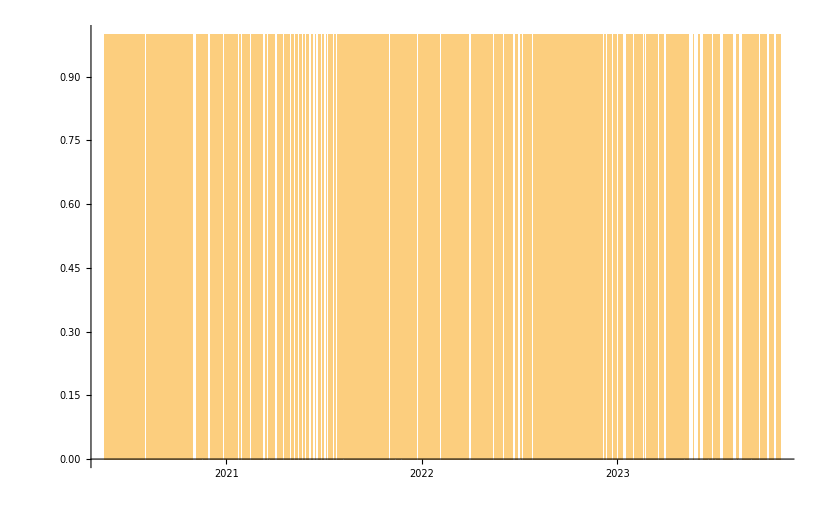

```mathematica
DateHistogram[data,"Day",ImageSize->Large]
```

```mathematica
data2=Transpose@{data,Table[1,Length@data]};
```

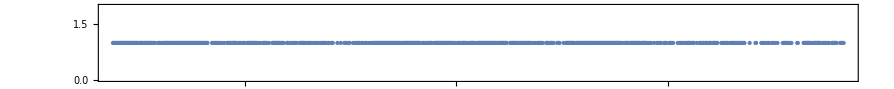

```mathematica
DateListPlot[data2,Joined->False,ImageSize->Large,PlotStyle->PointSize[Small],AspectRatio->1/10]
```

```mathematica
Export["/tmp/digits.txt",RealDigits[Pi,10,100000][[1,2;;]]]
```

/tmp/digits.txt